```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Projects\research\Diffusion-Lattice-Distribution-Set-Theory

```mathematica
Get["./base_package/SOHR_base.m"]
```

```mathematica
Names[$Context<>"*"]
```

{CalculateLimit,ExponentialBasis,ExponentialBasis$,GetExponentialBase,GetHMatrix,GetPathwayProbabilityVector,Hij,HMatrix,HMatrix$,i,j,l,LambdaCalculateLimit,LambdaExponentialBasis,LambdaGetExponentialBase,LambdaGetHMatrix,LambdaGetPathwayProbabilityVector,LambdaHij,LambdaHMatrix,LambdaPathProbV,LambdaPPV,LambdaPPV2,LambdaPPV2C1,LambdaPPV3,LambdaPPV3C1,LambdaToSubScriptExpression,m,n,NStep,output,output$,P,q,t,ToSubScriptExpression,λ,λ1,λ2,λ3,λ4,λ5}

# A⇌_k_1^k_1B type reaction network

```mathematica
HMatrix = GetHMatrix[5,5];
ExponentialBasis = GetExponentialBase[5];
HMatrix//MatrixForm
ExponentialBasis//MatrixForm
```

(1 | 0 | 0 | 0 | 0
k1/(-k1+k2) | k1/(k1-k2) | 0 | 0 | 0
(k1 k2)/((-k1+k2) (-k1+k3)) | (k1 k2)/((k1-k2) (-k2+k3)) | (k1 k2)/((k1-k3) (k2-k3)) | 0 | 0
(k1 k2 k3)/((-k1+k2) (-k1+k3) (-k1+k4)) | (k1 k2 k3)/((k1-k2) (-k2+k3) (-k2+k4)) | (k1 k2 k3)/((k1-k3) (k2-k3) (-k3+k4)) | (k1 k2 k3)/((k1-k4) (k2-k4) (k3-k4)) | 0
(k1 k2 k3 k4)/((-k1+k2) (-k1+k3) (-k1+k4) (-k1+k5)) | (k1 k2 k3 k4)/((k1-k2) (-k2+k3) (-k2+k4) (-k2+k5)) | (k1 k2 k3 k4)/((k1-k3) (k2-k3) (-k3+k4) (-k3+k5)) | (k1 k2 k3 k4)/((k1-k4) (k2-k4) (k3-k4) (-k4+k5)) | (k1 k2 k3 k4)/((k1-k5) (k2-k5) (k3-k5) (k4-k5)))

(ⅇ^(-k1 t)
ⅇ^(-k2 t)
ⅇ^(-k3 t)
ⅇ^(-k4 t)
ⅇ^(-k5 t))

```mathematica
PathProbV = HMatrix.ExponentialBasis;
```

```mathematica
Limit[Limit[Limit[PathProbV[[1]],k5->k3],k3->k1],k4->k2]
Limit[Limit[Limit[PathProbV[[2]],k5->k3],k3->k1],k4->k2]
Limit[Limit[Limit[PathProbV[[3]],k5->k3],k3->k1],k4->k2]
Limit[Limit[Limit[PathProbV[[4]],k5->k3],k3->k1],k4->k2]
Limit[Limit[Limit[PathProbV[[5]],k5->k3],k3->k1],k4->k2]
```

ⅇ^(-k1 t)

(ⅇ^(-k2 t) k1)/(k1-k2)+(ⅇ^(-k1 t) k1)/(-k1+k2)

(ⅇ^(-(k1+k2) t) k1 k2 (ⅇ^(k1 t)+ⅇ^(k2 t) (-1-k1 t+k2 t)))/(k1-k2)^2

(ⅇ^(-(k1+k2) t) k1^2 k2 (ⅇ^(k1 t) (-2+k1 t-k2 t)+ⅇ^(k2 t) (2+k1 t-k2 t)))/(k1-k2)^3

(ⅇ^(-(k1+k2) t) k1^2 k2^2 (2 ⅇ^(k1 t) (-3+k1 t-k2 t)+ⅇ^(k2 t) (6-4 k2 t+k1^2 t^2+k2^2 t^2-2 k1 t (-2+k2 t))))/(2 (k1-k2)^4)

```mathematica
PathProbV/.{k5->Subscript[k, 5],k4->Subscript[k, 4],k3->Subscript[k, 3],k2->Subscript[k, 2],k1->Subscript[k, 1]}//MatrixForm
```

(ⅇ^(-t k_1)
(ⅇ^(-t k_2) k_1)/(k_1-k_2)+(ⅇ^(-t k_1) k_1)/(-k_1+k_2)
(ⅇ^(-t k_3) k_1 k_2)/((k_1-k_3) (k_2-k_3))+(ⅇ^(-t k_1) k_1 k_2)/((-k_1+k_2) (-k_1+k_3))+(ⅇ^(-t k_2) k_1 k_2)/((k_1-k_2) (-k_2+k_3))
(ⅇ^(-t k_4) k_1 k_2 k_3)/((k_1-k_4) (k_2-k_4) (k_3-k_4))+(ⅇ^(-t k_1) k_1 k_2 k_3)/((-k_1+k_2) (-k_1+k_3) (-k_1+k_4))+(ⅇ^(-t k_2) k_1 k_2 k_3)/((k_1-k_2) (-k_2+k_3) (-k_2+k_4))+(ⅇ^(-t k_3) k_1 k_2 k_3)/((k_1-k_3) (k_2-k_3) (-k_3+k_4))
(ⅇ^(-t k_5) k_1 k_2 k_3 k_4)/((k_1-k_5) (k_2-k_5) (k_3-k_5) (k_4-k_5))+(ⅇ^(-t k_1) k_1 k_2 k_3 k_4)/((-k_1+k_2) (-k_1+k_3) (-k_1+k_4) (-k_1+k_5))+(ⅇ^(-t k_2) k_1 k_2 k_3 k_4)/((k_1-k_2) (-k_2+k_3) (-k_2+k_4) (-k_2+k_5))+(ⅇ^(-t k_3) k_1 k_2 k_3 k_4)/((k_1-k_3) (k_2-k_3) (-k_3+k_4) (-k_3+k_5))+(ⅇ^(-t k_4) k_1 k_2 k_3 k_4)/((k_1-k_4) (k_2-k_4) (k_3-k_4) (-k_4+k_5)))

```mathematica
PPV = PathProbV;
For[i=Length[PPV],i≥1,i--,
For[j=i-1,j≥1,j--,PPV⟦i⟧=CalculateLimit[PPV⟦i⟧,j+1,j]]
];
```

```mathematica
PPV/.{k1->Subscript[k, 1]}//MatrixForm
```

(ⅇ^(-t k_1)
ⅇ^(-t k_1) t k_1
1/2 ⅇ^(-t k_1) t^2 k_1^2
1/6 ⅇ^(-t k_1) t^3 k_1^3
1/24 ⅇ^(-t k_1) t^4 k_1^4)

## Has pattern of 1/(n!)ⅇ^(-k_1 t) k_1^n t^n, this is exactly the Poisson distribution Pr(N_t=n) =f(n; λt) =e^-λt/(n!)(λt)^n

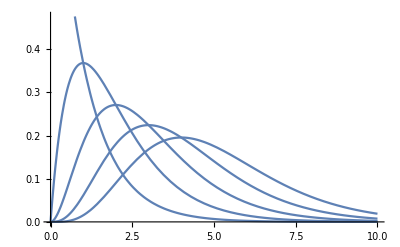

```mathematica
Plot[PPV/.k1->1.0,{t,0,10}]
```

```mathematica
(*Names[$Context<>"*"]*)
```

## Think of set {0,1,2,3,...} represent path length Pathway probability has form of p_n=c_n e^-k_nt, in continuous x-axis, the distribution function is P(x)=∑_nϵℕ P_n δ(x-n) The definition of characteristic function states that G(z)=⟨e^izX⟩=∫_I e^izx P(x)dx G(z)=∑_nϵℕ P_n e^izn G(z)=∑_nϵℕ c_n e^-k_nt e^izn

```mathematica
A={ⅇ^-λ1,(ⅇ^-λ2 λ1)/(λ1-λ2)+(ⅇ^-λ1 λ1)/(-λ1+λ2),(ⅇ^-λ3 λ1 λ2)/((λ1-λ3) (λ2-λ3))+(ⅇ^-λ1 λ1 λ2)/((-λ1+λ2) (-λ1+λ3))+(ⅇ^-λ2 λ1 λ2)/((λ1-λ2) (-λ2+λ3)),(ⅇ^-λ4 λ1 λ2 λ3)/((λ1-λ4) (λ2-λ4) (λ3-λ4))+(ⅇ^-λ1 λ1 λ2 λ3)/((-λ1+λ2) (-λ1+λ3) (-λ1+λ4))+(ⅇ^-λ2 λ1 λ2 λ3)/((λ1-λ2) (-λ2+λ3) (-λ2+λ4))+(ⅇ^-λ3 λ1 λ2 λ3)/((λ1-λ3) (λ2-λ3) (-λ3+λ4)),(ⅇ^-λ5 λ1 λ2 λ3 λ4)/((λ1-λ5) (λ2-λ5) (λ3-λ5) (λ4-λ5))+(ⅇ^-λ1 λ1 λ2 λ3 λ4)/((-λ1+λ2) (-λ1+λ3) (-λ1+λ4) (-λ1+λ5))+(ⅇ^-λ2 λ1 λ2 λ3 λ4)/((λ1-λ2) (-λ2+λ3) (-λ2+λ4) (-λ2+λ5))+(ⅇ^-λ3 λ1 λ2 λ3 λ4)/((λ1-λ3) (λ2-λ3) (-λ3+λ4) (-λ3+λ5))+(ⅇ^-λ4 λ1 λ2 λ3 λ4)/((λ1-λ4) (λ2-λ4) (λ3-λ4) (-λ4+λ5))};
A//MatrixForm
```

(ⅇ^-λ1
(ⅇ^-λ2 λ1)/(λ1-λ2)+(ⅇ^-λ1 λ1)/(-λ1+λ2)
(ⅇ^-λ3 λ1 λ2)/((λ1-λ3) (λ2-λ3))+(ⅇ^-λ1 λ1 λ2)/((-λ1+λ2) (-λ1+λ3))+(ⅇ^-λ2 λ1 λ2)/((λ1-λ2) (-λ2+λ3))
(ⅇ^-λ4 λ1 λ2 λ3)/((λ1-λ4) (λ2-λ4) (λ3-λ4))+(ⅇ^-λ1 λ1 λ2 λ3)/((-λ1+λ2) (-λ1+λ3) (-λ1+λ4))+(ⅇ^-λ2 λ1 λ2 λ3)/((λ1-λ2) (-λ2+λ3) (-λ2+λ4))+(ⅇ^-λ3 λ1 λ2 λ3)/((λ1-λ3) (λ2-λ3) (-λ3+λ4))
(ⅇ^-λ5 λ1 λ2 λ3 λ4)/((λ1-λ5) (λ2-λ5) (λ3-λ5) (λ4-λ5))+(ⅇ^-λ1 λ1 λ2 λ3 λ4)/((-λ1+λ2) (-λ1+λ3) (-λ1+λ4) (-λ1+λ5))+(ⅇ^-λ2 λ1 λ2 λ3 λ4)/((λ1-λ2) (-λ2+λ3) (-λ2+λ4) (-λ2+λ5))+(ⅇ^-λ3 λ1 λ2 λ3 λ4)/((λ1-λ3) (λ2-λ3) (-λ3+λ4) (-λ3+λ5))+(ⅇ^-λ4 λ1 λ2 λ3 λ4)/((λ1-λ4) (λ2-λ4) (λ3-λ4) (-λ4+λ5)))

```mathematica
B={ⅇ^-λ1,ⅇ^-λ2/(λ1-λ2)+ⅇ^-λ1/(-λ1+λ2),ⅇ^-λ3/((λ1-λ3) (λ2-λ3))+ⅇ^-λ1/((-λ1+λ2) (-λ1+λ3))+ⅇ^-λ2/((λ1-λ2) (-λ2+λ3)),ⅇ^-λ4/((λ1-λ4) (λ2-λ4) (λ3-λ4))+ⅇ^-λ1/((-λ1+λ2) (-λ1+λ3) (-λ1+λ4))+ⅇ^-λ2/((λ1-λ2) (-λ2+λ3) (-λ2+λ4))+ⅇ^-λ3/((λ1-λ3) (λ2-λ3) (-λ3+λ4)),ⅇ^-λ5/((λ1-λ5) (λ2-λ5) (λ3-λ5) (λ4-λ5))+ⅇ^-λ1 /((-λ1+λ2) (-λ1+λ3) (-λ1+λ4) (-λ1+λ5))+ⅇ^-λ2 /((λ1-λ2) (-λ2+λ3) (-λ2+λ4) (-λ2+λ5))+ⅇ^-λ3 /((λ1-λ3) (λ2-λ3) (-λ3+λ4) (-λ3+λ5))+ⅇ^-λ4/((λ1-λ4) (λ2-λ4) (λ3-λ4) (-λ4+λ5))};
B//MatrixForm
```

(ⅇ^-λ1
ⅇ^-λ2/(λ1-λ2)+ⅇ^-λ1/(-λ1+λ2)
ⅇ^-λ3/((λ1-λ3) (λ2-λ3))+ⅇ^-λ1/((-λ1+λ2) (-λ1+λ3))+ⅇ^-λ2/((λ1-λ2) (-λ2+λ3))
ⅇ^-λ4/((λ1-λ4) (λ2-λ4) (λ3-λ4))+ⅇ^-λ1/((-λ1+λ2) (-λ1+λ3) (-λ1+λ4))+ⅇ^-λ2/((λ1-λ2) (-λ2+λ3) (-λ2+λ4))+ⅇ^-λ3/((λ1-λ3) (λ2-λ3) (-λ3+λ4))
ⅇ^-λ5/((λ1-λ5) (λ2-λ5) (λ3-λ5) (λ4-λ5))+ⅇ^-λ1/((-λ1+λ2) (-λ1+λ3) (-λ1+λ4) (-λ1+λ5))+ⅇ^-λ2/((λ1-λ2) (-λ2+λ3) (-λ2+λ4) (-λ2+λ5))+ⅇ^-λ3/((λ1-λ3) (λ2-λ3) (-λ3+λ4) (-λ3+λ5))+ⅇ^-λ4/((λ1-λ4) (λ2-λ4) (λ3-λ4) (-λ4+λ5)))

```mathematica
Limit[Limit[Limit[Limit[B⟦1⟧,λ5->λ4],λ4->λ3],λ3->λ2],λ2->λ1]
Limit[Limit[Limit[Limit[B⟦2⟧,λ5->λ4],λ4->λ3],λ3->λ2],λ2->λ1]
Limit[Limit[Limit[Limit[B⟦3⟧,λ5->λ4],λ4->λ3],λ3->λ2],λ2->λ1]
Limit[Limit[Limit[Limit[B⟦4⟧,λ5->λ4],λ4->λ3],λ3->λ2],λ2->λ1]
Limit[Limit[Limit[Limit[B⟦5⟧,λ5->λ4],λ4->λ3],λ3->λ2],λ2->λ1]
```

ⅇ^-λ1

ⅇ^-λ1

ⅇ^-λ1/2

ⅇ^-λ1/6

ⅇ^-λ1/24

```mathematica
LC= Table[Limit[Limit[Limit[B⟦i⟧,λ5->λ3],λ4->λ2],λ3->λ1],{i,1,Length[B]}];
LC
```

{ⅇ^-λ1,ⅇ^-λ2/(λ1-λ2)+ⅇ^-λ1/(-λ1+λ2),(ⅇ^(-λ1-λ2) (ⅇ^λ1+ⅇ^λ2 (-1-λ1+λ2)))/(λ1-λ2)^2,(ⅇ^(-λ1-λ2) (ⅇ^λ1 (-2+λ1-λ2)+ⅇ^λ2 (2+λ1-λ2)))/(λ1-λ2)^3,(ⅇ^(-λ1-λ2) (2 ⅇ^λ1 (-3+λ1-λ2)+ⅇ^λ2 (6+λ1^2-2 λ1 (-2+λ2)-4 λ2+λ2^2)))/(2 (λ1-λ2)^4)}

```mathematica
LD={ⅇ^λ1,-ⅇ^λ2+ⅇ^λ1, (ⅇ^λ1+ⅇ^λ2 (-1-λ1+λ2)), (ⅇ^λ1 (-2+λ1-λ2)+ⅇ^λ2 (2+λ1-λ2)),(2 ⅇ^λ1 (-3+λ1-λ2)+ⅇ^λ2 (6+λ1^2-2 λ1 (-2+λ2)-4 λ2+λ2^2))};
LD//MatrixForm
```

(ⅇ^λ1
ⅇ^λ1-ⅇ^λ2
ⅇ^λ1+ⅇ^λ2 (-1-λ1+λ2)
ⅇ^λ1 (-2+λ1-λ2)+ⅇ^λ2 (2+λ1-λ2)
2 ⅇ^λ1 (-3+λ1-λ2)+ⅇ^λ2 (6+λ1^2-2 λ1 (-2+λ2)-4 λ2+λ2^2))

```mathematica
C1=Table[Coefficient[LD⟦i⟧,ⅇ^λ1],{i,1,Length[LD]}];
C2=Table[Coefficient[LD⟦i⟧,ⅇ^λ2],{i,1,Length[LD]}];
C1//MatrixForm
C2//MatrixForm
```

(1
1
1
-2+λ1-λ2
-6+2 λ1-2 λ2)

(0
-1
-1-λ1+λ2
2+λ1-λ2
6+4 λ1+λ1^2-4 λ2-2 λ1 λ2+λ2^2)

```mathematica
D1=Table[C1⟦i⟧/.{λ1->λ2+x}//Simplify,{i,1,Length[C1]}]
```

{1,1,1,-2+x,2 (-3+x)}

```mathematica
D1=Table[C2⟦i⟧/.{λ1->λ2+x}//Simplify,{i,1,Length[C2]}]
```

{0,-1,-1-x,2+x,6+4 x+x^2}